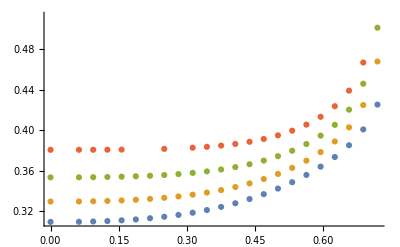

```mathematica
A12={{0,3.130919},{0.062500,3.118583},{0.093750,3.128569},{0.125000,3.140804},{0.156250,3.157232},{0.187500,3.177726},{0.218750,3.202008},{0.250000,3.229841},{0.281250,3.261050},{0.312500,3.295530},{0.343750,3.333230},{0.375000,3.374158},{0.406250,3.418376},{0.437500,3.465994},{0.468750,3.517178},{0.500000,3.572145},{0.531250,3.631171},{0.562500,3.694593},{0.593750,3.762816},{0.625000,3.836326},{0.656250,3.915695},{0.687500,4.001601},{0.718750,4.094843}};
A22={{0,3.883919},{0.062500,3.873624},{0.093750,3.899067},{0.125000,3.925200},{0.156250,3.956988},{0.187500,3.994756},{0.218750,4.038323},{0.250000,4.087486},{0.281250,4.142106},{0.312500,4.202131},{0.343750,4.267588},{0.375000,4.338587},{0.406250,4.415310},{0.437500,4.498014},{0.468750,4.587026},{0.500000,4.682747},{0.531250,4.785647},{0.562500,4.896279},{0.593750,5.015274},{0.625000,5.143356},{0.656250,5.281348},{0.687500,5.430188},{0.718750,5.590935}};
A32={{0,4.575125},{0.062500,4.567850},{0.093750,4.609620},{0.125000,4.650274},{0.156250,4.697861},{0.187500,4.753201},{0.218750,4.816247},{0.250000,4.886855},{0.281250,4.964939},{0.312500,5.050510},{0.343750,5.143678},{0.375000,5.244651},{0.406250,5.353731},{0.437500,5.471309},{0.468750,5.597866},{0.500000,5.733964},{0.531250,5.880254},{0.562500,6.037473},{0.593750,6.206446},{0.625000,6.388096},{0.656250,6.583450},{0.687500,6.793650},{0.718750,7.019950}};
A42={{0,5.238260},{0.062500,5.234179},{0.093750,5.292505},{0.125000,5.347859},{0.156250,5.411392},{0.187500,29.776953},{0.218750,27.780364},{0.250000,5.659143},{0.281250,27.771327},{0.312500,5.871897},{0.343750,5.992808},{0.375000,6.123783},{0.406250,6.265240},{0.437500,6.417702},{0.468750,6.581795},{0.500000,6.758237},{0.531250,6.947843},{0.562500,7.151518},{0.593750,7.370261},{0.625000,7.605168},{0.656250,7.857437},{0.687500,8.128374},{0.718750,8.419387}};
A13={{0,2.821520},{0.062500,2.809064},{0.093750,2.818764},{0.125000,2.830537},{0.156250,2.846298},{0.187500,2.865888},{0.218750,2.888998},{0.250000,2.915355},{0.281250,2.944750},{0.312500,2.977034},{0.343750,3.012116},{0.375000,3.049955},{0.406250,3.090561},{0.437500,3.133992},{0.468750,3.180352},{0.500000,3.229794},{0.531250,3.282521},{0.562500,3.338774},{0.593750,3.398805},{0.625000,3.462784},{0.656250,3.530525},{0.687500,3.600789},{0.718750,3.669519}};
A23={{0,3.554412},{0.062500,3.544038},{0.093750,3.569275},{0.125000,3.595076},{0.156250,3.626382},{0.187500,3.663493},{0.218750,3.706200},{0.250000,3.754266},{0.281250,3.807514},{0.312500,3.865844},{0.343750,3.929234},{0.375000,3.997730},{0.406250,4.071446},{0.437500,4.150554},{0.468750,4.235288},{0.500000,4.325936},{0.531250,4.422834},{0.562500,4.526352},{0.593750,4.636842},{0.625000,4.754451},{0.656250,4.878483},{0.687500,5.005250},{0.718750,5.122973}};
A33={{0,4.221702},{0.062500,4.214383},{0.093750,4.256033},{0.125000,4.296490},{0.156250,4.343786},{0.187500,4.398720},{0.218750,4.461221},{0.250000,4.531113},{0.281250,4.608273},{0.312500,4.692665},{0.343750,4.784343},{0.375000,4.883447},{0.406250,4.990199},{0.437500,5.104893},{0.468750,5.227889},{0.500000,5.359607},{0.531250,5.500513},{0.562500,5.651095},{0.593750,5.811792},{0.625000,5.982777},{0.656250,6.163127},{0.687500,6.347681},{0.718750,6.518592}};
A43={{0,4.857593},{0.062500,4.853503},{0.093750,4.911798},{0.125000,4.967093},{0.156250,5.030530},{0.187500,5.103403},{0.218750,5.185784},{0.250000,5.277567},{0.281250,5.378690},{0.312500,5.489188},{0.343750,5.609195},{0.375000,5.738951},{0.406250,5.878787},{0.437500,6.029117},{0.468750,6.190432},{0.500000,6.363283},{0.531250,6.548265},{0.562500,6.745985},{0.593750,6.956969},{0.625000,7.181414},{0.656250,7.418258},{0.687500,7.661431},{0.718750,7.889006}};
AA1=A12-A13*Table[{0,1},{i,0,22}];
AA2=A22-A23*Table[{0,1},{i,0,22}];
AA3=A32-A33*Table[{0,1},{i,0,22}];
AA4=A42-A43*Table[{0,1},{i,0,22}];
ListPlot[{AA1,AA2, AA3,AA4}]
```

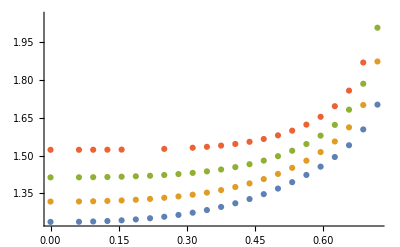

```mathematica
AAA13=A13*Table[{1,4},{i,0,22}];
AAA12=A12*Table[{1,4},{i,0,22}];
AAA23=A23*Table[{1,4},{i,0,22}];
AAA22=A22*Table[{1,4},{i,0,22}];
AAA33=A33*Table[{1,4},{i,0,22}];
AAA32=A32*Table[{1,4},{i,0,22}];
AAA43=A43*Table[{1,4},{i,0,22}];
AAA42=A42*Table[{1,4},{i,0,22}];
AAA1=AAA12-AAA13*Table[{0,1},{i,0,22}];
AAA2=AAA22-AAA23*Table[{0,1},{i,0,22}];
AAA3=AAA32-AAA33*Table[{0,1},{i,0,22}];
AAA4=AAA42-AAA43*Table[{0,1},{i,0,22}];
ListPlot[{AAA1,AAA2, AAA3,AAA4}]
```

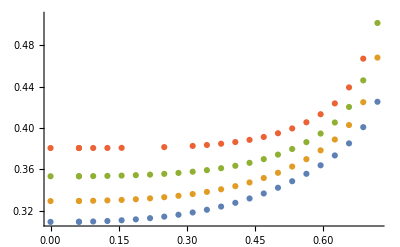

```mathematica
a={{0,3.130919},{0.062500,3.118583},{0.062500,3.118583},{0.093750,3.128569},{0.125000,3.140804},{0.156250,3.157232},{0.187500,3.177726},{0.218750,3.202008},{0.250000,3.229841},{0.281250,3.261050},{0.312500,3.295530},{0.343750,3.333230},{0.375000,3.374158},{0.406250,3.418376},{0.437500,3.465994},{0.468750,3.517178},{0.500000,3.572145},{0.531250,3.631171},{0.562500,3.694593},{0.593750,3.762816},{0.625000,3.836326},{0.656250,3.915695},{0.687500,4.001601},{0.718750,4.094843}};
a2={{0,3.883919},{0.062500,3.873624},{0.062500,3.873624},{0.093750,3.899067},{0.125000,3.925200},{0.156250,3.956988},{0.187500,3.994756},{0.218750,4.038323},{0.250000,4.087486},{0.281250,4.142106},{0.312500,4.202131},{0.343750,4.267588},{0.375000,4.338587},{0.406250,4.415310},{0.437500,4.498014},{0.468750,4.587026},{0.500000,4.682747},{0.531250,4.785647},{0.562500,4.896279},{0.593750,5.015274},{0.625000,5.143356},{0.656250,5.281348},{0.687500,5.430188},{0.718750,5.590935}};
a3={{0,4.575125},{0.062500,4.567850},{0.062500,4.567850},{0.093750,4.609620},{0.125000,4.650274},{0.156250,4.697861},{0.187500,4.753201},{0.218750,4.816247},{0.250000,4.886855},{0.281250,4.964939},{0.312500,5.050510},{0.343750,5.143678},{0.375000,5.244651},{0.406250,5.353731},{0.437500,5.471309},{0.468750,5.597866},{0.500000,5.733964},{0.531250,5.880254},{0.562500,6.037473},{0.593750,6.206446},{0.625000,6.388096},{0.656250,6.583450},{0.687500,6.793650},{0.718750,7.019950}};
a4={{0,5.238260},{0.062500,5.234179},{0.062500,5.234179},{0.093750,5.292505},{0.125000,5.347859},{0.156250,5.411392},{0.187500,29.776953},{0.218750,27.780364},{0.250000,5.659143},{0.281250,27.771327},{0.312500,5.871897},{0.343750,5.992808},{0.375000,6.123783},{0.406250,6.265240},{0.437500,6.417702},{0.468750,6.581795},{0.500000,6.758237},{0.531250,6.947843},{0.562500,7.151518},{0.593750,7.370261},{0.625000,7.605168},{0.656250,7.857437},{0.687500,8.128374},{0.718750,8.419387}};
aa={{0,2.821520},{0.062500,2.809064},{0.062500,2.809064},{0.093750,2.818764},{0.125000,2.830537},{0.156250,2.846298},{0.187500,2.865888},{0.218750,2.888998},{0.250000,2.915355},{0.281250,2.944750},{0.312500,2.977034},{0.343750,3.012116},{0.375000,3.049955},{0.406250,3.090561},{0.437500,3.133992},{0.468750,3.180352},{0.500000,3.229794},{0.531250,3.282521},{0.562500,3.338774},{0.593750,3.398805},{0.625000,3.462784},{0.656250,3.530525},{0.687500,3.600789},{0.718750,3.669519}};
aa2={{0,3.554412},{0.062500,3.544038},{0.062500,3.544038},{0.093750,3.569275},{0.125000,3.595076},{0.156250,3.626382},{0.187500,3.663493},{0.218750,3.706200},{0.250000,3.754266},{0.281250,3.807514},{0.312500,3.865844},{0.343750,3.929234},{0.375000,3.997730},{0.406250,4.071446},{0.437500,4.150554},{0.468750,4.235288},{0.500000,4.325936},{0.531250,4.422834},{0.562500,4.526352},{0.593750,4.636842},{0.625000,4.754451},{0.656250,4.878483},{0.687500,5.005250},{0.718750,5.122973}};
aa3={{0,4.221702},{0.062500,4.214383},{0.062500,4.214383},{0.093750,4.256033},{0.125000,4.296490},{0.156250,4.343786},{0.187500,4.398720},{0.218750,4.461221},{0.250000,4.531113},{0.281250,4.608273},{0.312500,4.692665},{0.343750,4.784343},{0.375000,4.883447},{0.406250,4.990199},{0.437500,5.104893},{0.468750,5.227889},{0.500000,5.359607},{0.531250,5.500513},{0.562500,5.651095},{0.593750,5.811792},{0.625000,5.982777},{0.656250,6.163127},{0.687500,6.347681},{0.718750,6.518592}};
aa4={{0,4.857593},{0.062500,4.853503},{0.062500,4.853503},{0.093750,4.911798},{0.125000,4.967093},{0.156250,5.030530},{0.187500,5.103403},{0.218750,5.185784},{0.250000,5.277567},{0.281250,5.378690},{0.312500,5.489188},{0.343750,5.609195},{0.375000,5.738951},{0.406250,5.878787},{0.437500,6.029117},{0.468750,6.190432},{0.500000,6.363283},{0.531250,6.548265},{0.562500,6.745985},{0.593750,6.956969},{0.625000,7.181414},{0.656250,7.418258},{0.687500,7.661431},{0.718750,7.889006}};
A1=a-aa*Table[{0,1},{i,0,23}];
A2=a2-aa2*Table[{0,1},{i,0,23}];
A3=a3-aa3*Table[{0,1},{i,0,23}];
A4=a4-aa4*Table[{0,1},{i,0,23}];
ListPlot[{A1,A2, A3,A4}]
```

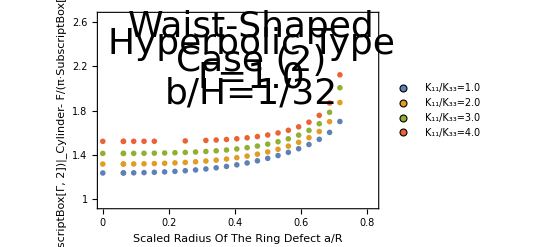

```mathematica
AA1=A1*Table[{1,4},{i,0,23}];
AA2=A2*Table[{1,4},{i,0,23}];
AA3=A3*Table[{1,4},{i,0,23}];
AA4=A4*Table[{1,4},{i,0,23}];
ListPlot[{AA1,AA2,AA3,AA4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{1,1.4,1.8,2.2,2.6},None},{{0,0.2, 0.4, 0.6, 0.8},None}}, PlotRange->{{0,0.82},{0.95,2.65}},FrameLabel->{{"F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Cylinder- F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Waist", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.45,2.55}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.45,2.4}],Text[Style["Case (2)",Directive[Black,36]],{0.45,2.25}],Text[Style["Γ=1.0",Directive[Black,36]],{0.45,2.1}],Text[Style["b/H=1/32",Directive[Black,36]],{0.45,1.95}]}]
```